```mathematica
n=99;
Subscript[V, 1]=1;
M=1;
K=1;
TIME=5000;
df=0.5;
steps=20;

Subscript[F, yay][x_,k_]=k*(x[t]+ϵ*x[t]^3);

For[i=2,i<n+2,++i,Subscript[m, i]=0.1/n]
For[i=2,i<n+2,++i,Subscript[ω, i]=2/n*i]
For[i=2,i<n+2,++i,Subscript[k, i]=Subscript[ω, i]^2*Subscript[m, i]]
Clear[i];
```

```mathematica
IFk=Integrate[Subscript[F, yay][x,k],x[t]];
T =0.5* M *Subscript[x, 1]'[t]^2 + 0.5*Sum[Subscript[m, i]*D[Subscript[x, i][t],t]^2, {i,2,n+1}];
V1=IFk/.{x[t]->Subscript[x, 1][t],k->K};
V2=Sum[IFk/.{x[t]->Subscript[x, i][t]-Subscript[x, 1][t],k->Subscript[k, i]},{i, 2, n+1}];
V=V1+V2;
L=T-V;
Eqs=Table[ D[L,Subscript[x, i][t]]-D[D[L,D[Subscript[x, i][t],t]],t]==0 , {i,1,n+1} ];
AllVars=Table[Subscript[x, i],{i,1,n+1}];
InitialCon=Flatten[{Table[Subscript[x, i][0]==0,{i,1,n+1}],Table[Subscript[x, i]'[0]==0,{i,2,n+1}],Subscript[x, 1]'[0]==1}];

For[cnt=1,cnt<steps+1,cnt++,
ϵ=0.0001*(cnt-1);
numsol=NDSolve[Flatten[Join[Eqs,InitialCon]],AllVars,{t,0,TIME},MaxSteps->∞,PrecisionGoal->12,AccuracyGoal->12,Method->"ExplicitRungeKutta"];
a=Abs[Fourier[Table[(Subscript[x, 1]/.numsol[[1]])[i*df],{i,0,TIME/df}]]];
b=Table[{N[i/TIME*2π],20*Log[a[[i]]]},{i,1,TIME/df}];
p1[cnt]=Plot[Evaluate[Subscript[x, 1][t]/.numsol[[1]]],{t,0,TIME},PlotRange->{{-50,500},All},ImageSize->320,PlotLabel->"Displacement Of Primary Zoomed"];
p2[cnt]=Plot[Evaluate[Subscript[x, 1][t]/.numsol[[1]]],{t,0,TIME},PlotRange->{{-50,TIME},All},ImageSize->320,PlotLabel->"Displacement Of Primary"];
p3[cnt]=ListLinePlot[b,PlotRange->{{0,2.5},All} ,PlotLabel->StringJoin["FFT of Displacement of Primary ϵ=",ToString[ϵ]],AxesLabel->{"Frequency ω (rad/s)","20Log |H|(ω)"},ImageSize->320]
]
```

```mathematica
Table[{p1[i],p2[i],p3[i]},{i,1,steps}]//MatrixForm
Export["/Users/Gediz/Desktop/LinerFreqDist-HardeninSpring-IncreaseNonLinearity.jpg",%,ImageSize->150]
```

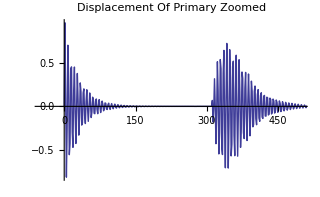
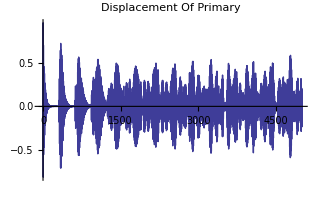
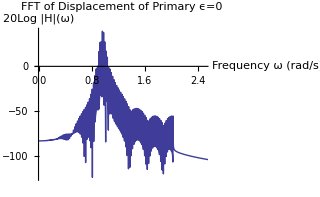
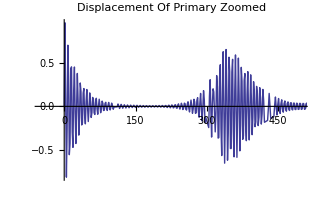
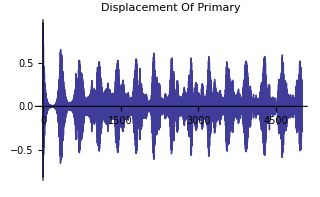
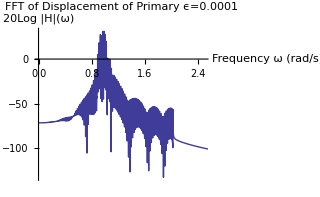
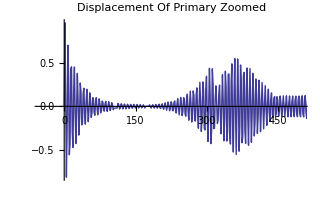
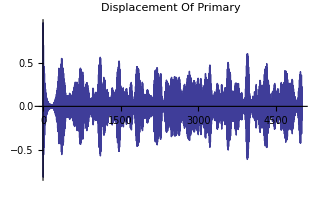
```mathematica
({{-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}})
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}